```mathematica
Quit
```

Ancillary file of the paper “Tidal Love numbers and quasi-normal modes of the Schwarzschild-Hernquist black hole”
by Sumanta Chakraborty, Geoffrey Compère and Ludovico Machet. 

This notebook was written by G . Compère

### 1. The three dimensionless parameters

Dimensionful constants being used to define the dimensionless quantities

```mathematica
parsec=3.08 10^16 m;
MassSun=1.99 10^30 kg;
cVal=299792458 m/sec;
GVal=6.67 10^(-11) m^3/sec^2/kg;
GMSun=GVal MassSun/cVal^2;
GevOverc2=1.79 10^(-27) kg;
cm=10^(-2)m;
```

The three parameters that serve as the baseline model:

```mathematica
MDMOverMBHVal=10^6
MBHOverMSunVal=10^6
rsOverGMBHVal= 2*10^4 parsec/(MDMOverMBHVal GMSun)
```

1000000

1000000

4.17103×10^11

### 2. Functions defining the Schwarzschild-Hernquist model

We define all functions and function parameters to be dimensionless, by scaling with the typical scale of the central supermassive black hole

```mathematica
(* rOverGMBH, rsOverGMBH and MBHOverMSun are DIMENSIONLESS *)
```

```mathematica
λ[MDMOverMBH_,rsOverGMBH_,MBHOverMSun_]:= (MDMOverMBH/MDMOverMBHVal)^(1/3)(MBHOverMSun/MBHOverMSunVal)^(-5/3)(rsOverGMBH/rsOverGMBHVal)^(-2/3)
```

Here AMBH2 is the A parameter times the mass of the central black hole squared .

```mathematica
mSHOverMBH[rOverGMBH_,MDMOverMBH_,rsOverGMBH_,MBHOverMSun_]:= 1+8λ[MDMOverMBH,rsOverGMBH,MBHOverMSun]AMBH2 π xsp^4 4^(-q-w+2)(rOverGMBH-4)^(w+1)(rOverGMBH+xsp)^q xsp^(-q)(xsp+4)^(q+w+1)(rOverGMBH+xsp)^(-q-w-1)/2/(w+1)/(xsp+4)^4 Hypergeometric2F1[w+1,q+w-2,w+2,-(rOverGMBH-4)xsp/(4(rOverGMBH+xsp))]HeavisideTheta[rOverGMBH-4]/.{xsp-> 2 rsOverGMBH MDMOverMBH}/.{w->2.45,q-> 2.33,α->0.33,β-> -1.66,γ-> -0.67, AMBH2-> 1.85 10^22 GevOverc2/cm^3 GVal^3/cVal^6  MBHOverMSunVal^2 MassSun^2 (MBHOverMSun/MBHOverMSunVal)^2}
```

The mass function is actually very simple - looking

```mathematica
mSHOverMBH[r,MDMOverMBHVal,rsOverGMBHVal,MBHOverMSunVal]
```

1+(2.78767×10^53 (-4+r)^3.45 HeavisideTheta[-4+r] Hypergeometric2F1[2.78,3.45,4.45,(2.08551×10^17 (4-r))/(8.34206×10^17+r)])/((8.34206×10^17+r)^3.45)

The plot matches with Figure 2 of the paper:

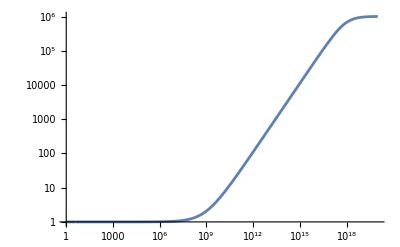

```mathematica
LogLogPlot[mSHOverMBH[rOverGMBHVal,MDMOverMBHVal,rsOverGMBHVal,MBHOverMSunVal],{rOverGMBHVal,1,10^20},PlotRange->All]
```

I take here the definitions from the draft with physical dimensions for ρ and Pt :

```mathematica
ρ[rOverGMBH_,MDMOverMBH_,rsOverGMBH_,MBHOverMSun_]:=
1/GVal^3 cVal^6 D[mSHOverMBH[rOverGMBH,MDMOverMBHVal,rsOverGMBHVal,MBHOverMSunVal],rOverGMBH]2/π/8/(MBHOverMSun MassSun)^2/(rOverGMBH )^2
```

```mathematica
Pt[rOverGMBH_,MDMOverMBH_,rsOverGMBH_,MBHOverMSun_] :=mSHOverMBH[rOverGMBH,MDMOverMBH,rsOverGMBH,MBHOverMSun]ρ[rOverGMBH,MDMOverMBH,rsOverGMBH,MBHOverMSun]/2/(rOverGMBH-2 mSHOverMBH[rOverGMBH,MDMOverMBH,rsOverGMBH,MBHOverMSun])
```

Here is the actual definition of f and m of the draft: (here x=1/r)

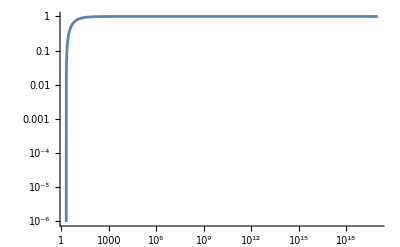

```mathematica
f[rOverGMBH_,MDMOverMBH_,rsOverGMBH_,MBHOverMSun_] :=Exp[-NIntegrate[2 mSHOverMBH[1/xOverGMBH,MDMOverMBH,rsOverGMBH,MBHOverMSun]/(1-2 xOverGMBH mSHOverMBH[1/xOverGMBH,MDMOverMBH,rsOverGMBH,MBHOverMSun]),{xOverGMBH,0,1/rOverGMBH}]]
LogLogPlot[f[rOverGMBH,MDMOverMBHVal,rsOverGMBHVal,MBHOverMSunVal] ,{rOverGMBH,2,10^20},PlotRange-> All]
```

### 3. CHECK DOMINANT and STRONG energy conditions for astrophysical baseline model

```mathematica
m^3/kg ρ[r,MDMOverMBHVal,rsOverGMBHVal,MBHOverMSunVal]
ρVal[r_]:=Evaluate[%]
```

1/r^2 4.91621×10^7 ((2.78767×10^53 (-4+r)^3.45 DiracDelta[-4+r] Hypergeometric2F1[2.78,3.45,4.45,(2.08551×10^17 (4-r))/(8.34206×10^17+r)])/((8.34206×10^17+r)^3.45)-(9.61745×10^53 (-4+r)^3.45 HeavisideTheta[-4+r] Hypergeometric2F1[2.78,3.45,4.45,(2.08551×10^17 (4-r))/(8.34206×10^17+r)])/((8.34206×10^17+r)^4.45)+(9.61745×10^53 (-4+r)^2.45 HeavisideTheta[-4+r] Hypergeometric2F1[2.78,3.45,4.45,(2.08551×10^17 (4-r))/(8.34206×10^17+r)])/((8.34206×10^17+r)^3.45)+(6.0082×10^53 (-4+r)^3.45 (-(2.08551×10^17 (4-r))/((8.34206×10^17+r)^2)-(2.08551×10^17)/(8.34206×10^17+r)) HeavisideTheta[-4+r] Hypergeometric2F1[3.78,4.45,5.45,(2.08551×10^17 (4-r))/(8.34206×10^17+r)])/((8.34206×10^17+r)^3.45))

```mathematica
m^3/kg Pt[r,MDMOverMBHVal,rsOverGMBHVal,MBHOverMSunVal]
PtVal[r_]:=Evaluate[%]
```

(2.45811×10^7 (1+(2.78767×10^53 (-4+r)^3.45 HeavisideTheta[-4+r] Hypergeometric2F1[2.78,3.45,4.45,(2.08551×10^17 (4-r))/(8.34206×10^17+r)])/((8.34206×10^17+r)^3.45)) ((2.78767×10^53 (-4+r)^3.45 DiracDelta[-4+r] Hypergeometric2F1[2.78,3.45,4.45,(2.08551×10^17 (4-r))/(8.34206×10^17+r)])/((8.34206×10^17+r)^3.45)-(9.61745×10^53 (-4+r)^3.45 HeavisideTheta[-4+r] Hypergeometric2F1[2.78,3.45,4.45,(2.08551×10^17 (4-r))/(8.34206×10^17+r)])/((8.34206×10^17+r)^4.45)+(9.61745×10^53 (-4+r)^2.45 HeavisideTheta[-4+r] Hypergeometric2F1[2.78,3.45,4.45,(2.08551×10^17 (4-r))/(8.34206×10^17+r)])/((8.34206×10^17+r)^3.45)+(6.0082×10^53 (-4+r)^3.45 (-(2.08551×10^17 (4-r))/((8.34206×10^17+r)^2)-(2.08551×10^17)/(8.34206×10^17+r)) HeavisideTheta[-4+r] Hypergeometric2F1[3.78,4.45,5.45,(2.08551×10^17 (4-r))/(8.34206×10^17+r)])/((8.34206×10^17+r)^3.45)))/(r^2 (r-2 (1+(2.78767×10^53 (-4+r)^3.45 HeavisideTheta[-4+r] Hypergeometric2F1[2.78,3.45,4.45,(2.08551×10^17 (4-r))/(8.34206×10^17+r)])/((8.34206×10^17+r)^3.45))))

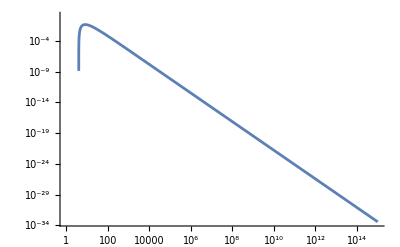

```mathematica
LogLogPlot[ρVal[rOverGMBH],{rOverGMBH,1,10^15}]
```

The order of magnitude of Pt is 5 lower than ρ, so all energy conditions are obeyed.

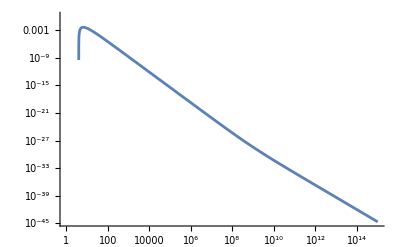

```mathematica
LogLogPlot[PtVal[rOverGMBH],{rOverGMBH,1,10^15}]
```

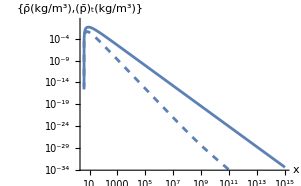

```mathematica
P1b=LogLogPlot[Re[ρVal[rOverGMBH]],{rOverGMBH,4,10^15}];
P2b=LogLogPlot[Re[PtVal[rOverGMBH]],{rOverGMBH,4,10^15},PlotStyle->Dashed];
Show[P1b,P2b,AxesLabel->{HoldForm[x],HoldForm[{ρ̄[kg/m^3],Subscript[p̄, t][kg/m^3]}]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

### 4. CHECK PHOTON SPHERES

We see from the plot of f/r^2 that there is a single point where the radial derivative of f/r^2  vanishes: this is rOverGMBH=3, the location of the standard light-ring.

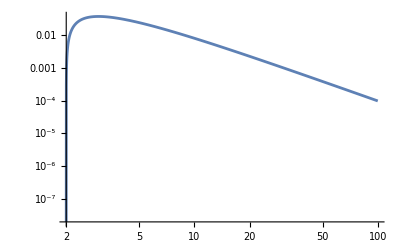

```mathematica
LogLogPlot[f[rOverGMBH,MDMOverMBHVal,rsOverGMBHVal,MBHOverMSunVal]/rOverGMBH^2 ,{rOverGMBH,2,100},PlotRange-> All]
```

```mathematica
{MDMOverMBHVal,rsOverGMBHVal,MBHOverMSunVal}
```

{1000000,4.17103×10^11,1000000}

After a simple algebra the condition (f/r^2)’=0 is equivalent to r-3m=0 for the Einstein model without radial pressure. In fact r-3m=-(r-2m)r^3/(2f)D[f/r^2,r], so the 0 of r-3m is the 0 of D[f/r^2,r]. We can check that we recover again the light-ring radius for the baseline model:

```mathematica
FindRoot[(rOverGMBH-3 mSHOverMBH[rOverGMBH,MDMOverMBHVal,rsOverGMBHVal,MBHOverMSunVal]),{rOverGMBH,1000}]
```

{rOverGMBH→3.}

```mathematica
D[(r-3m[r])/r/(r-2m[r]),r]//Simplify
```

(6 r m[r]-6 m[r]^2-r^2 (1+m'[r]))/(r^2 (r-2 m[r])^2)

The function r-3m is always 0 at r=3 because the matter starts to kick in only at r=4. At very large r, m goes to a constant while r grows so r-3m goes to +∞. So, if we have a simple additional zero, we actually will have two: a light-ring and anti-light ring

If we scale down rsOverGMBHVal  by 10 orders of magnitude, we find 3 zeros:  (2 light-rings and 1 anti-light ring)

First 2 zeros :

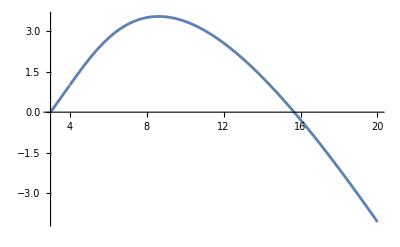

```mathematica
Plot[(rOverGMBH-3 mSHOverMBH[rOverGMBH,MDMOverMBHVal,rsOverGMBHVal/10^10,MBHOverMSunVal]),{rOverGMBH,3,20},PlotRange-> All]
```

Third far zero :

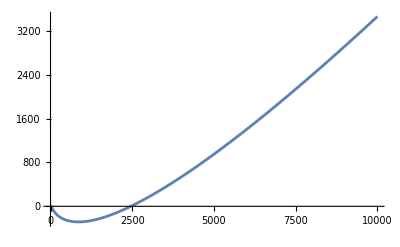

```mathematica
Plot[(rOverGMBH-3 mSHOverMBH[rOverGMBH,MDMOverMBHVal,rsOverGMBHVal/10^10,MBHOverMSunVal]),{rOverGMBH,1,10000},PlotRange-> All]
```

The first one is the standard light-ring. To understand the second and third zeros we need the sign of (f/r^2)’’ . Since computing f is numerically demanding, we use the following trick: at the location of a root r such that (f/r^2)’=0, we have that (f/r^2)’’=-2f/r^2 ((r-3m)/(r(r-2m)))’ so the sign of (f/r^2)’’ is the sign of ((-r+3m)/(r(r-2m)))’.

```mathematica
fct[rOverGMBH_,MDMOverMBH_,rsOverGMBH_,MBHOverMSun_]:=(-rOverGMBH+3mSHOverMBH[rOverGMBH,MDMOverMBH,rsOverGMBH,MBHOverMSun])/rOverGMBH/(rOverGMBH-2mSHOverMBH[rOverGMBH,MDMOverMBH,rsOverGMBH,MBHOverMSun])
```

We get a minus sign for the derivative of the function around r=3, so r=3 is a light-ring (V’’<0, unstable)

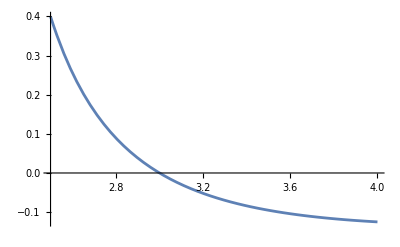

```mathematica
Plot[fct[rOverGMBH,MDMOverMBHVal,rsOverGMBHVal/10^10,MBHOverMSunVal],{rOverGMBH,2.5,4},PlotRange-> All]
```

We get a plus sign around r=15.6, so r=15.6 is a anti-light-ring (V’’>0, stable)

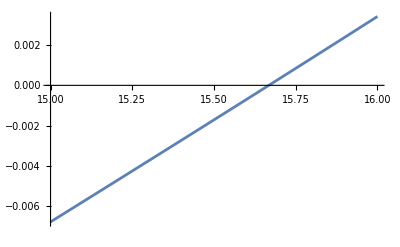

```mathematica
Plot[fct[rOverGMBH,MDMOverMBHVal,rsOverGMBHVal/10^10,MBHOverMSunVal],{rOverGMBH,15,16},PlotRange-> All]
```

We get a minus sign around r=2500, so r=2500 is a light-ring (V’’<0, unstable)

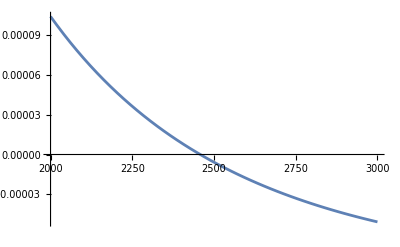

```mathematica
Plot[fct[rOverGMBH,MDMOverMBHVal,rsOverGMBHVal/10^10,MBHOverMSunVal],{rOverGMBH,2000,3000},PlotRange-> All]
```

So we found a triplet of parameters such that we have a lightring ; antilightring ; lightring structure. 
Let’s call the corresponding parameters the “baseline double lightring case” 
Let us check how to scale the parameters such that we keep that structure :

This is again the baseline double light ring case :

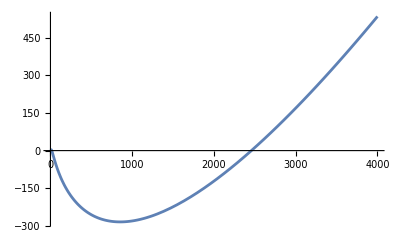

```mathematica
Plot[Re[(rOverGMBH-3 mSHOverMBH[rOverGMBH,MDMOverMBHVal ,rsOverGMBHVal/10^10,MBHOverMSunVal])],{rOverGMBH,1,4000},PlotRange-> All]
```

Here is the solution up to a scaling:

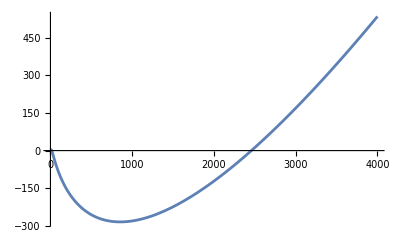

```mathematica
Plot[Re[(rOverGMBH-3 mSHOverMBH[rOverGMBH,MDMOverMBHVal 100,rsOverGMBHVal/10^9,MBHOverMSunVal])],{rOverGMBH,1,4000},PlotRange-> All]
```

### 5. CHECK DOMINANT energy condition for the double light ring baseline model

```mathematica
factor=5/2/10^10;
```

```mathematica
m^3/kg ρ[r,MDMOverMBHVal,rsOverGMBHVal factor,MBHOverMSunVal]//Simplify
ρVal[r_]:=Evaluate[%]
```

1/r^2 4.91621×10^7 HeavisideTheta[-4+r] ((-(9.61745×10^53 (-4+r)^3.45)/((8.34206×10^17+r)^4.45)+(9.61745×10^53 (-4+r)^2.45)/((8.34206×10^17+r)^3.45)) Hypergeometric2F1[2.78,3.45,4.45,(8.34206×10^17-2.08551×10^17 r)/(8.34206×10^17+r)]-(1.04528×10^89 (-4+r)^3.45 Hypergeometric2F1[3.78,4.45,5.45,(8.34206×10^17-2.08551×10^17 r)/(8.34206×10^17+r)])/((8.34206×10^17+r)^5.45))

```mathematica
m^3/kg Pt[r,MDMOverMBHVal,rsOverGMBHVal factor,MBHOverMSunVal]//Simplify
PtVal[r_]:=Evaluate[%]
```

(HeavisideTheta[-4+r] (2.45811×10^7 (2.08551×10^8+r)^3.45+1.28857×10^34 (-4+r)^3.45 HeavisideTheta[-4+r] Hypergeometric2F1[2.78,3.45,4.45,(2.08551×10^8-5.21379×10^7 r)/(2.08551×10^8+r)]) ((-(9.61745×10^53 (-4+r)^3.45)/((8.34206×10^17+r)^4.45)+(9.61745×10^53 (-4+r)^2.45)/((8.34206×10^17+r)^3.45)) Hypergeometric2F1[2.78,3.45,4.45,(8.34206×10^17-2.08551×10^17 r)/(8.34206×10^17+r)]-(1.04528×10^89 (-4+r)^3.45 Hypergeometric2F1[3.78,4.45,5.45,(8.34206×10^17-2.08551×10^17 r)/(8.34206×10^17+r)])/((8.34206×10^17+r)^5.45)))/(r^2 ((-2.+r) (2.08551×10^8+r)^3.45-1.04842×10^27 (-4+r)^3.45 HeavisideTheta[-4+r] Hypergeometric2F1[2.78,3.45,4.45,(2.08551×10^8-5.21379×10^7 r)/(2.08551×10^8+r)]))

Dominant Energy condition

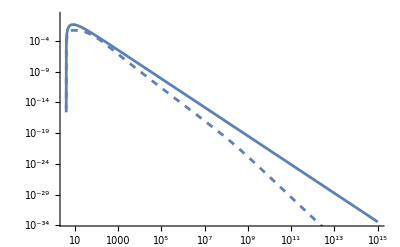

```mathematica
P1=LogLogPlot[Re[ρVal[rOverGMBH]],{rOverGMBH,4,10^15}];
P2=LogLogPlot[Re[PtVal[rOverGMBH]],{rOverGMBH,4,10^15},PlotStyle->Dashed];
Show[P1,P2]
```

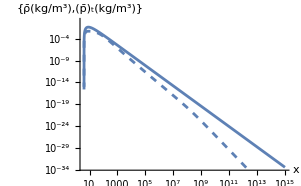

```mathematica
Show[P1,P2,AxesLabel->{HoldForm[x],HoldForm[{ρ̄[kg/m^3],Subscript[p̄, t][kg/m^3]}]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

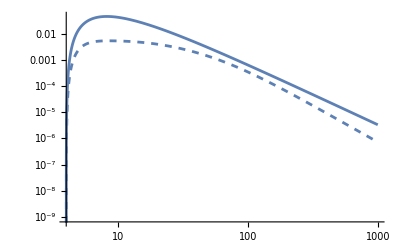

```mathematica
P1=LogLogPlot[Re[ρVal[rOverGMBH]],{rOverGMBH,4,1000}];
P2=LogLogPlot[Re[PtVal[rOverGMBH]],{rOverGMBH,4,1000},PlotStyle->Dashed];
Show[P1,P2]
```

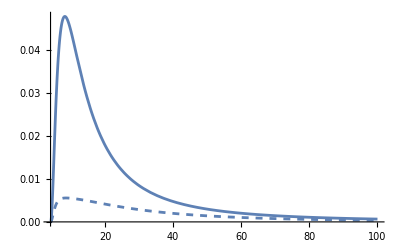

```mathematica
P1=Plot[Re[ρVal[rOverGMBH]],{rOverGMBH,4,100}];
P2=Plot[Re[PtVal[rOverGMBH]],{rOverGMBH,4,100},PlotStyle->Dashed];
Show[P1,P2]
```

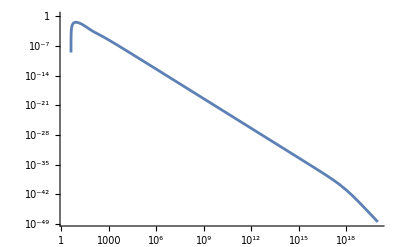

```mathematica
LogLogPlot[Re[ρVal[rOverGMBH]-PtVal[rOverGMBH]],{rOverGMBH,2,10^20}]
```